## Problem 1 E

Set Constants

```mathematica
x[λ_] = Log[10, λ];
xmin = x[2.5*10^-21];
xmid = x[2.5*10^-11];
xmax = N[x[10^6]];
tmin := .5
temerge := 1
trequired := 3.5
```

Define non normalized function :

```mathematica
PMxD[x_] := 1/(xmax-xmin)(1-Exp[-10^x(temerge-tmin)])/(1-Exp[-10^x(trequired - tmin)]);
```

Take the limit for the lower half of the distribution :

```mathematica
Limit[PMxD[x], x->-∞]
```

0.00626518

Now find the normalization constant through integration over the whole range of λ:

```mathematica
NIntegrate[%11, {x, xmin, xmid}]+NIntegrate[PMxD[x], {x, xmid, xmax}]
```

0.349394

Define and plot normalized function :

```mathematica
PMxDNorm[x_] := 1/(.349394(xmax-xmin))(1-Exp[-10^x(temerge-tmin)])/(1-Exp[-10^x(trequired - tmin)]);
```

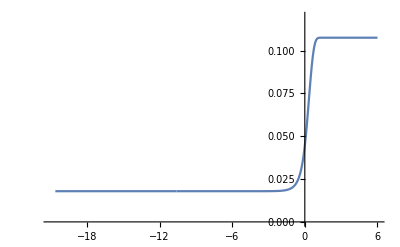

```mathematica
Show[Plot[PMxDNorm[x], {x, xmid, xmax},PlotRange->{{-21,6},{0,.12}}],Plot[%194, {x,xmin,xmid}]]
```

Quick check for normalization :

```mathematica
Limit[PMxDNorm[x], x->-∞]
```

0.0179316

```mathematica
NIntegrate[%71, {x, xmin, xmid}]+NIntegrate[PMxDNorm[x], {x,xmid, xmax}]
```

1.

Now solve for P_l and P_m:

```mathematica
pL = NIntegrate[%71, {x,xmin, xmid}]
```

0.179316

```mathematica
pM = NIntegrate[PMxDNorm[x], {x, xmid, xmax}]
```

0.820686

## Problem 1 F

This new data point calls for new λ values:

```mathematica
x2[λ_] = Log[10, λ];
xmin2= x2[5*10^-21];
xmid2 = x2[5*10^-11];
xmax2 = x2[10^6];
tmin2 := .5
temerge2 := 1
temergeMars := .8
trequired2 := 3.5
```

We now consider the probability of life on both Earth and Mars.  Since abiogenesis on each planet occurs independently:

P(Life_Earth, Life_Mars) = P_(Life on Earth)(λ, t) P_(Life on Mars)(λ, t)

T_required remains the same because we are obseving the life from earth.  Thus, no intelligent life is assumed so no need to consider time for evolution wrt Mars (Earth observed life).  However, t_emergeMars=.8 GYr.

```mathematica
PMxD2[x_] := 1/(xmax2-xmin2)((1-Exp[-10^x(temerge2-tmin2)])(1-Exp[-10^x(temergeMars-tmin2)]))/(1-Exp[-10^x(trequired2 - tmin2)]);
```

```mathematica
N[Limit[PMxD2[x], x->-∞]]
```

0.

Find the normalization constant :

```mathematica
NIntegrate[%16, {x,xmin2, xmid2}]+NIntegrate[PMxD2[x],  {x, xmid2, xmax2}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.210398

```mathematica
PMxD2Norm[x_] := 1/(.210398(xmax2-xmin2))((1-Exp[-10^x(temerge2-tmin2)]) (1-Exp[-10^x(temergeMars-tmin2)]))/(1-Exp[-10^x(trequired2 - tmin2)]);
```

```mathematica
Limit[PMxD2Norm[x], x->-∞]
```

0.

Now solve for P_l and P_m:

```mathematica
NIntegrate[%143, {x, xmin2, xmid2}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[PMxD2Norm[x], {x, xmid2, xmax2}]
```

0.999998